```mathematica
ClearAll["Global`*"]
```

```mathematica
$PrePrint=#/.{Csc[z_]:>1/Defer@Sin[z],Sec[z_]:>1/Defer@Cos[z]}&;
```

```mathematica
eqx=m x''[t]==F Cos[φ[t]]+μ Sin[φ[t]];
eqy=m y''[t]==F Sin[φ[t]]-μ Cos[φ[t]];
eqK=y'[t]==x'[t]Tan[φ[t]];
μNEW=μ/.First[Solve[eqy,μ]]//FullSimplify;
```

```mathematica
μNEW=μ/.First[Solve[eqy,μ]]//FullSimplify;
eqxNEW=eqx/.μ->μNEW;
eqKder=Dt[x'[t] Sin[φ[t]]-y'[t] Cos[φ[t]]==0,t];
DD=y''[t]/.First@Solve[eqKder,y''[t]];
DD=DD/.y'[t]->y'[t]/.First@Solve[eqK,y'[t]];
eqSOLx=eqxNEW/.y''[t]->DD//Simplify
```

(m (Tan[φ[t]] x'[t] φ'[t]+x''[t]))/Cos[φ[t]]^2==F/Cos[φ[t]]

```mathematica
μNEW=μ/.First[Solve[eqx,μ]]//FullSimplify;
eqxNEW=eqy/.μ->μNEW;
eqKder=Dt[x'[t] Sin[φ[t]]-y'[t] Cos[φ[t]]==0,t];
DD=x''[t]/.First@Solve[eqKder,x''[t]];
DD=DD/.x'[t]->x'[t]/.First@Solve[eqK,x'[t]];
eqSOLy=eqxNEW/.x''[t]->DD//Simplify
```

(m y''[t])/Sin[φ[t]]^2==(F+(m Cot[φ[t]] y'[t] φ'[t])/Sin[φ[t]])/Sin[φ[t]]

```mathematica
T=1;
φ[t_]=Sin[(2π)/T t-0.0001];
F=100; m=1;
```

```mathematica
solx=NDSolve[{eqSOLx,x[0]==0,x'[0]==0},x[t],{t,0,2}];
soly=NDSolve[{eqSOLy,y[0]==0,y'[0]==0},y[t],{t,0,2}];
```

NDSolve::ndsz: At t == 0.500016, step size is effectively zero; singularity or stiff system suspected.

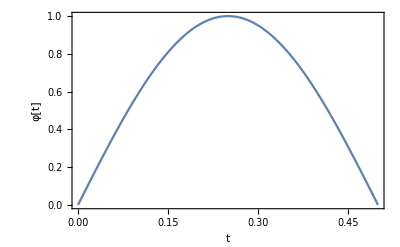

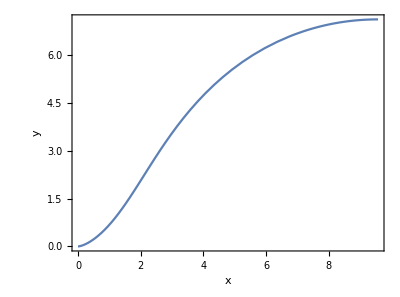

```mathematica
xSol[t_]=x[t]/.First[solx];
ySol[t_]=y[t]/.First[soly];
Plot[φ[t],{t,0,.5},Frame->True,FrameLabel->{t,"φ[t]"}]
ParametricPlot[{xSol[t],ySol[t]},{t,0,.5},Frame->True,FrameLabel->{x,y}]
```